```mathematica
Quit
```

## MC Values (from Jess)

```mathematica
SetDirectory["/Users/rachelwilliams1/Desktop/Cosmography f(R) project/Mathematica codes/MC Results"];
```

```mathematica
mcmcFiles=<|"Model 1"->"mcmc_parameter_summary_model_1_20000steps.csv","Model 2"->"mcmc_parameter_summary_model_2_20000steps.csv","Model 3"->"mcmc_parameter_summary_model_3_50000steps.csv"|>;
```

```mathematica
paramColumnMap=<|"H0_mean"->"H0","q0_mean"->"q0","j0_mean"->"j0","Om0_mean"->"Om0","eps_mean"->"eps","wDE0_mean"->"wDE0","wDE0p_mean"->"wDE0p"|>;
```

```mathematica
(*Build the nested association for a single model's CSV file*)
BuildModelParams[file_String]:=Module[{data,header,rows},data=Import[file,"Data"];
header=First[data];
rows=Rest[data];
Association[Map[Function[row,Module[{assocFull,datasetName},assocFull=AssociationThread[header->row];
datasetName=assocFull["dataset"];
datasetName->Association[KeyValueMap[Function[{oldKey,newKey},newKey->assocFull[oldKey]],paramColumnMap]]]],rows]]];
```

```mathematica
(*Master nested association:allParams["Model 1"]["DESI"]-><|"H0"->...,...|>*)
allParams=Association[KeyValueMap[Function[{modelName,file},modelName->BuildModelParams[file]],mcmcFiles]];
```

```mathematica
(* ============================================================*)
(*Convenience accessors*)
(* ============================================================*)

(*List available models*)
AvailableModels[]=Keys[allParams];
AvailableDatasets[model_String]:=Keys[allParams[model]];
```

```mathematica
AvailableModels[]
```

{Model 1,Model 2,Model 3}

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
(*(*Main getter:GetParams["Model 1","DESI"]->Association of params*)
GetParams[model_String,dataset_String]:=Module[{},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
allParams[model][dataset]];

GetParams::nomodel="Model `1` not found. Available models: `2`";
GetParams::nodataset="Dataset `1` not found for `2`. Available datasets: `3`";*)
```

```mathematica
(*Map model name->jModel function*)
jModelMap=<|"Model 1"->j1,"Model 2"->j2,"Model 3"->j3|>;
```

```mathematica
(*Main getter:GetParams["Model 1","DESI"]->Association of params,including "j"*)
GetParams[model_String,dataset_String]:=Module[{baseParams},If[!KeyExistsQ[allParams,model],Message[GetParams::nomodel,model,AvailableModels[]];
Return[$Failed]];
If[!KeyExistsQ[allParams[model],dataset],Message[GetParams::nodataset,dataset,model,AvailableDatasets[model]];
Return[$Failed]];
baseParams=allParams[model][dataset];
Append[baseParams,"j"->jModelMap[model]]];
```

### Model 1:

#### Desi Values

```mathematica
params1a=GetParams["Model 1","DESI"];
params1a["q0"]
params1a["Om0"]
params1a["eps"]
params1a["H0"]
```

-0.517033

0.498537

-0.0258394

68.2919

```mathematica
(*H01a=68.29192059313633;
q01a=-0.5170327771473278;
j01a=0.9625363652579005;
Ωm01a=0.4985365526609583;
ϵ1a=-0.025839351696166715;
wDE01a=-1.3514167286778105;*)
```

```mathematica
params10a=GetParams["Model 1","Planck + Union3 + Pantheon+ + DESY5"];
params10a["q0"]
params10a["Om0"]
params10a["eps"]
params10a["H0"]
```

-0.516172

0.31252

0.00132349

67.7409

### Model 2:

#### Desi Values

```mathematica
params2a=GetParams["Model 2","DESI"];
params2a["q0"]
params2a["Om0"]
params2a["eps"]
params2a["H0"]
```

-0.49883

0.491401

-0.100239

68.5342

```mathematica
H02a=68.53416748702578;
q02a=-0.49882983918505364;
j02a=0.8997606059127958;
Ωm02a=0.4914005086938241;
ϵ2a=-0.025839351696166715;
wDE02a=-1.3078293508597978;
```

### Model 3:

#### Desi Values

```mathematica
H03a=68.05462677945144;
q03a=-0.48266330038260274;
j03a=0.8033876955633561;
Ωm03a=0.5039105165387399;
ϵ3a=0.06671817784473298;
wDE03a=-1.3283914786225075;
```

## Equations

```mathematica
zPlot=10;
zinitial=50;
```

#### Defining the system of equations

```mathematica
dx= (1+z)x'[z]-(x[z]^2-x[z](2+q[z])-2-2q[z]+3Ω[z])==0;
dΩ=(1+z)Ω'[z]-Ω[z](x[z]+1-2q[z])==0;
dq=(1+z)q'[z]- (j[z]-q[z]-2 q[z]^2)==0;
dj= (1+z)j'[z]- (-s[z]-j[z](2+3q[z]))==0;
ds=(1+z)s'[z]- (-l[z]-s[z](3+4q[z]))==0;
dEh=(1+z)Eh'[z]- Eh[z](1+q[z])==0;
dH=(1+z)H'[z]- H[z](1+q[z])==0;
```

Autonomous system of equations
N=-ln(1+z) -> (1+z)d/dz = -d/dN

```mathematica
dxn= x'[n]+(x[n]^2-x[n](2+q[n])-2-2q[n]+3Ω[n])==0;
dΩn=Ω'[n]+Ω[n](x[n]+1-2q[n])==0;
dqn=q'[n]+ (j[n]-q[n]-2 q[n]^2)==0;
djn= j'[n]+ (-s[n]-j[n](2+3q[n]))==0;
dsn=s'[n]+ (-l[n]-s[n](3+4q[n]))==0;
dEhn=Eh'[n]+ Eh[n](1+q[n])==0;
dHn=H'[n]+ H[n](1+q[n])==0;
```

```mathematica
Fx[x_,Ω_,q_]:=-(x^2-x (2+q)-2-2 q+3 Ω);
FΩ[x_,Ω_,q_]:=-Ω (x+1-2 q);
Fq[q_,j_]:=-(j-q-2 q^2);
```

#### Models of j

```mathematica
j0[z_]=1;
j1[z_]=1+3ϵ(1+q[z]);
j2[z_]=1+ϵ;
j3[z_]=1+3ϵ(q[z]-1/2);
```

## Phase Space Analysis:

## Determining stability of fixed points

#### General fixed points for each model and specified dataset

```mathematica
FixedPointsStability[model_String,dataset_String]:=
Module[{params,epsVal,jExpr,jAlg,fps,Jac,classify,stabilityGrid},
params=GetParams[model,dataset];
epsVal=params["eps"];
jExpr=params["j"][n];

Block[{ϵ},ϵ=epsVal;
jAlg=jExpr/. q[n]->q;(*turn into algebraic expression in q*)
fps=NSolve[{Fx[x,Ω,q]==0,FΩ[x,Ω,q]==0,Fq[q,jAlg]==0},{x,Ω,q},Reals];

Jac[x_,Ω_,q_]=D[{Fx[x,Ω,q],FΩ[x,Ω,q],Fq[q,jAlg]},{{x,Ω,q}}];

classify[pt_]:=Module[{vals,eig,type},vals={x,Ω,q}/. pt;
eig=Eigenvalues[Jac@@vals]//N;
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];
{vals,eig,type}];
stabilityGrid=Grid[Prepend[classify/@fps,{"(x*, Ω*, q*)","Eigenvalues","Type"}],Frame->All];];
<|"model"->model,"dataset"->dataset,"eps"->epsVal,"fixedPoints"->fps,"stabilityGrid"->stabilityGrid|>];
```

```mathematica
fixedPointResults=Association[Map[Function[model,model->Association[Map[#->FixedPointsStability[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

```mathematica
fixedPointResults["Model 1"]["DESI"]["stabilityGrid"]
```

(x*, Ω*, q*) | Eigenvalues | Type
{-3.,-4.,-1.} | {4.,-3.,3.} | Saddle
{1.,0.,-1.} | {-4.,-3.,-1.} | Stable node/spiral
{0.,0.,-1.} | {-3.,-3.,1.} | Saddle
{3.33702,0.,0.461241} | {-4.21279,-3.41454,2.84496} | Saddle
{-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
{-0.875777,0.,0.461241} | {4.21279,2.84496,0.798259} | Unstable

### Matter dominated fixed points

#### Matter dominated fixed point selection modules

```mathematica
(* ============================================================*)
(*Extract the matter-dominated fixed point:the one closest to (x,Ω,q)=(0,1,1/2),the eps->0 EdS limit*)
(* ============================================================*)
ExtractMatterDominatedFP[fps_List]:=Module[{target,distances,bestIdx},
target={0,1,1/2};
distances=Map[Function[pt,Module[{vals},vals={x,Ω,q}/. pt;
Norm[N[vals]-N[target]]]],fps];
bestIdx=First[Ordering[distances,1]];
fps[[bestIdx]]];
```

```mathematica
MatterDominatedFP[model_String,dataset_String]:=
Module[{fpResult,fps,bestFP,vals,eig,eigvecs,type,Jac,jAlg,epsVal},
fpResult=FixedPointsStability[model,dataset];

fps=fpResult["fixedPoints"];
epsVal=fpResult["eps"];
bestFP=ExtractMatterDominatedFP[fps];
vals={x,Ω,q}/. bestFP;

Block[{ϵ},ϵ=epsVal;
jAlg=GetParams[model,dataset]["j"][n]/. q[n]->q;
Jac[xx_,OOmega_,qq_]=D[{Fx[xx,OOmega,qq],FΩ[xx,OOmega,qq],Fq[qq,jAlg]},{{xx,OOmega,qq}}];
{eig,eigvecs}=Eigensystem[Jac@@vals]//N;];
type=Which[AllTrue[eig,Re[#]<0&],"Stable node/spiral",AllTrue[eig,Re[#]>0&],"Unstable",True,"Saddle"];

<|"model"->model,"dataset"->dataset,"eps"->epsVal,"x"->vals[[1]],"Ω"->vals[[2]],"q"->vals[[3]],"eigenvalues"->eig,"eigenvectors"->eigvecs,"type"->type|>];
```

```mathematica
matterDominatedFPs=Association[Map[Function[model,model->Association[Map[#->MatterDominatedFP[model,#]&,AvailableDatasets[model]]]],AvailableModels[]]];
```

#### Model 1 results

```mathematica
Grid[Prepend[Table[
{
dataset,
{matterDominatedFPs["Model 1"][dataset]["x"],matterDominatedFPs["Model 1"][dataset]["Ω"],matterDominatedFPs["Model 1"][dataset]["q"]},
matterDominatedFPs["Model 1"][dataset]["eigenvalues"],
matterDominatedFPs["Model 1"][dataset]["type"]
},

{dataset,AvailableDatasets["Model 1"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0775181,0.908561,0.461241} | {3.41454,2.84496,-0.798259} | Saddle
Union3 | {-0.1625,0.806015,0.41875} | {3.44554,2.675,-0.70179} | Saddle
Pantheon+ | {-0.180312,0.784218,0.409844} | {3.452,2.63938,-0.681533} | Saddle
DESY5 | {-0.128173,0.847727,0.435914} | {3.43305,2.74365,-0.740793} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.187075,0.775913,0.406463} | {3.45445,2.62585,-0.673838} | Saddle
Planck | {0.0288443,1.03351,0.514422} | {3.37532,3.05769,-0.91859} | Saddle
Planck + Union3 | {0.0196617,1.02287,0.509831} | {3.37873,3.03932,-0.908219} | Saddle
Planck + Pantheon+ | {0.0128663,1.01498,0.506433} | {3.38124,3.02573,-0.900542} | Saddle
Planck + DESY5 | {0.0165391,1.01925,0.50827} | {3.37988,3.03308,-0.904691} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00397048,1.00463,0.501985} | {3.38453,3.00794,-0.890489} | Saddle

#### Model 2 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 2"][dataset]["x"],matterDominatedFPs["Model 2"][dataset]["Ω"],matterDominatedFPs["Model 2"][dataset]["q"]},matterDominatedFPs["Model 2"][dataset]["eigenvalues"],matterDominatedFPs["Model 2"][dataset]["type"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {-0.0683851,0.919438,0.465807} | {3.41119,2.86323,-0.808608} | Saddle
Union3 | {-0.171988,0.794417,0.414006} | {3.44898,2.65602,-0.691001} | Saddle
Pantheon+ | {-0.207,0.751359,0.3965} | {3.46166,2.586,-0.651156} | Saddle
DESY5 | {-0.144586,0.827833,0.427707} | {3.43903,2.71083,-0.722151} | Saddle
Union3 + Pantheon+ + DESY5 | {-0.223659,0.730728,0.388171} | {3.46767,2.55268,-0.632178} | Saddle
Planck | {0.0304847,1.03541,0.515242} | {3.37472,3.06097,-0.920443} | Saddle
Planck + Union3 | {0.0214876,1.02499,0.510744} | {3.37805,3.04298,-0.910281} | Saddle
Planck + Pantheon+ | {0.0146289,1.01703,0.507314} | {3.38059,3.02926,-0.902533} | Saddle
Planck + DESY5 | {0.0184722,1.02149,0.509236} | {3.37917,3.03694,-0.906875} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.00556607,1.00649,0.502783} | {3.38394,3.01113,-0.892292} | Saddle

#### Model 3 results

```mathematica
Grid[Prepend[Table[{dataset,{matterDominatedFPs["Model 3"][dataset]["x"],matterDominatedFPs["Model 3"][dataset]["Ω"],matterDominatedFPs["Model 3"][dataset]["q"]},matterDominatedFPs["Model 3"][dataset]["eigenvalues"],matterDominatedFPs["Model 3"][dataset]["type"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","{x*,Ω*,q*}","Eigenvalues","Type"}],Frame->All]
```

Dataset | {x*,Ω*,q*} | Eigenvalues | Type
DESI | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Pantheon+ | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle
Planck + Union3 + Pantheon+ + DESY5 | {0.,1.,0.5} | {3.386,3.,-0.886001} | Saddle

## Background Solution

```mathematica
SetDirectory@NotebookDirectory[];
```

## Obtaining Background solutions q(z) and E(z)

### Obtaining q(z)

```mathematica
SolveForq[model_String,dataset_String]:=
Module[{params,odeQ,sol},
params=GetParams[model,dataset];
odeQ={dq/. j->params["j"]/. ϵ->params["eps"],q[0]==params["q0"]};
sol=NDSolve[odeQ,q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
q/. sol[[1]]];
```

```mathematica
qSolAllSets1=Association[Map[#->SolveForq["Model 1",#]&,AvailableDatasets["Model 1"]]];
qSolAllSets2=Association[Map[#->SolveForq["Model 2",#]&,AvailableDatasets["Model 2"]]];
qSolAllSets3=Association[Map[#->SolveForq["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

```mathematica
qSolAllSets3["DESI"][0]
```

-0.482663

#### Model 1, All datasets

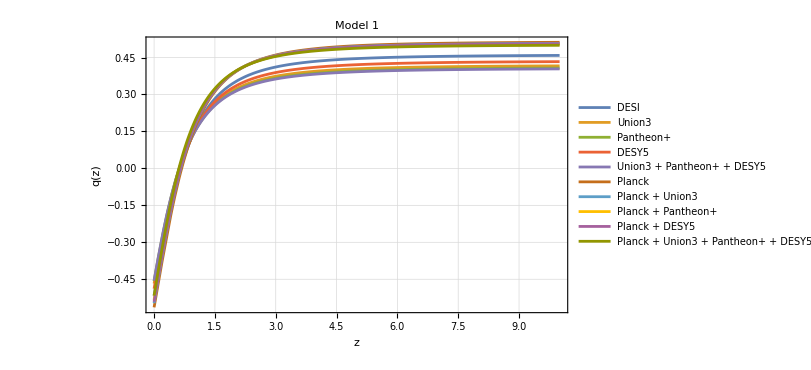

```mathematica
Plot[Evaluate[Table[qSolAllSets1[d][z],{d,Keys[qSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 2, All datasets

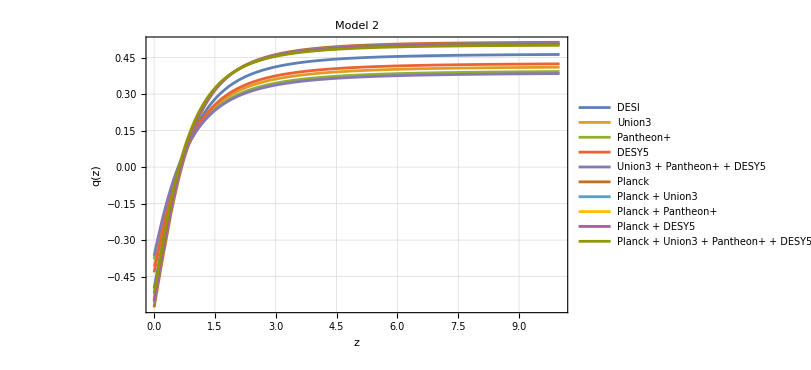

```mathematica
Plot[Evaluate[Table[qSolAllSets2[d][z],{d,Keys[qSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets2],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

#### Model 3, All datasets

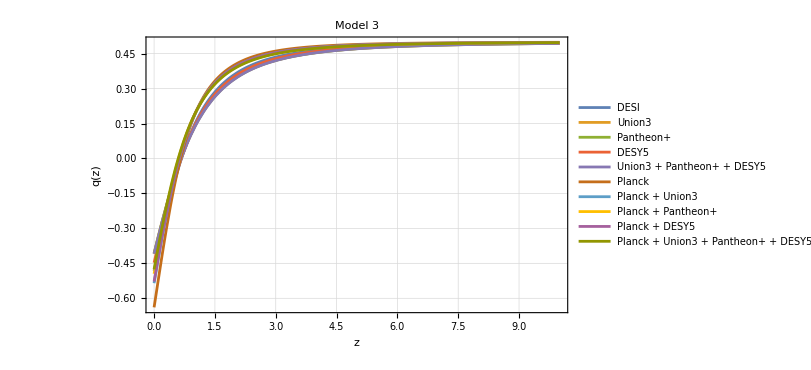

```mathematica
Plot[Evaluate[Table[qSolAllSets3[d][z],{d,Keys[qSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[qSolAllSets3],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.55,0.25}],Frame->True,FrameLabel->{"z","q(z)"},PlotRange->All,PlotLabel->"Model 3",GridLines->Automatic,ImageSize->600]
```

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

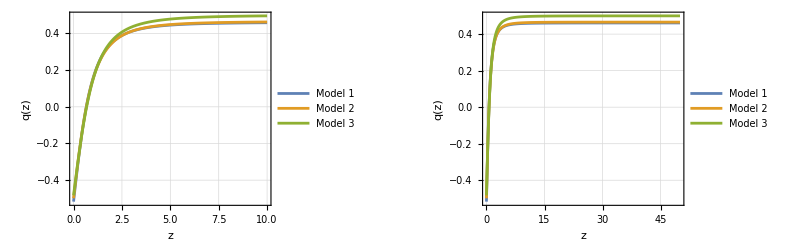

```mathematica
GraphicsRow[{
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","q(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{qSolAllSets1[DataSetPlot][z],qSolAllSets2[DataSetPlot][z],qSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","q(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

### Obtaining E(z)

```mathematica
SolveForEh[model_String,dataset_String]:=
Module[{params,qFn,odeEh,sol},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];

odeEh={(dEh/. q->qFn)/. ϵ->params["eps"],Eh[0]==1};
sol=NDSolve[odeEh,Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10];
Eh/. sol[[1]]];
```

```mathematica
hSolAllSets1=Association[Map[#->SolveForEh["Model 1",#]&,AvailableDatasets["Model 1"]]];
hSolAllSets2=Association[Map[#->SolveForEh["Model 2",#]&,AvailableDatasets["Model 2"]]];
hSolAllSets3=Association[Map[#->SolveForEh["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

#### Model 1, All datasets

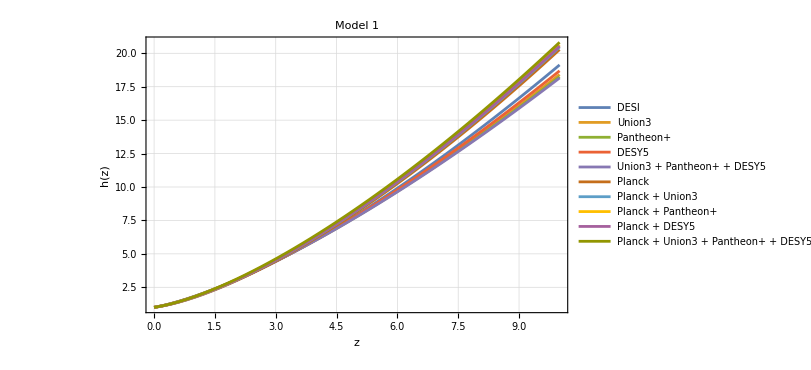

```mathematica
Plot[Evaluate[Table[hSolAllSets1[d][z],{d,Keys[hSolAllSets1]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 1",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets1[d][zinitial]},{d,Keys[hSolAllSets1]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 179.793
Union3 | 162.133
Pantheon+ | 158.461
DESY5 | 168.956
Union3 + Pantheon+ + DESY5 | 156.878
Planck | 206.816
Planck + Union3 | 207.34
Planck + Pantheon+ | 207.775
Planck + DESY5 | 207.497
Planck + Union3 + Pantheon+ + DESY5 | 208.335

#### Model 2, All datasets

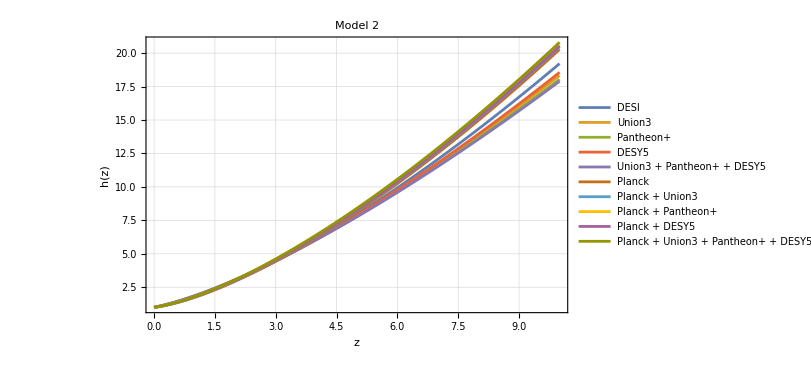

```mathematica
Plot[Evaluate[Table[hSolAllSets2[d][z],{d,Keys[hSolAllSets2]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 2",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets2[d][zinitial]},{d,Keys[hSolAllSets2]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 181.849
Union3 | 160.166
Pantheon+ | 153.453
DESY5 | 165.652
Union3 + Pantheon+ + DESY5 | 150.278
Planck | 207.077
Planck + Union3 | 207.547
Planck + Pantheon+ | 207.897
Planck + DESY5 | 207.696
Planck + Union3 + Pantheon+ + DESY5 | 208.451

#### Model 3, All datasets

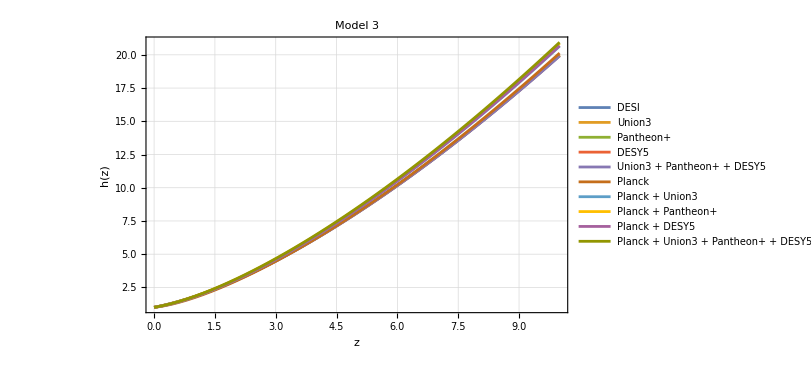

```mathematica
Plot[Evaluate[Table[hSolAllSets3[d][z],{d,Keys[hSolAllSets3]}]],{z,0,zPlot},PlotLegends->Placed[LineLegend[Keys[hSolAllSets1],LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&),LegendLayout->{"Column",2}],{0.45,0.8}],Frame->True,FrameLabel->{"z","h(z)"},PlotLabel->"Model 3",PlotRange->All,GridLines->Automatic,ImageSize->600]
```

```mathematica
TableForm[Table[{d,hSolAllSets3[d][zinitial]},{d,Keys[hSolAllSets3]}],TableHeadings->{None,{"Dataset","h(zInitial)"}}]
```

Dataset | h(zInitial)
DESI | 198.845
Union3 | 199.151
Pantheon+ | 198.85
DESY5 | 198.781
Union3 + Pantheon+ + DESY5 | 198.323
Planck | 200.875
Planck + Union3 | 206.051
Planck + Pantheon+ | 208.017
Planck + DESY5 | 206.363
Planck + Union3 + Pantheon+ + DESY5 | 208.88

#### Plotting for a specific dataset

```mathematica
AvailableDatasets["Model 1"]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

```mathematica
DataSetPlot=AvailableDatasets["Model 1"][[1]]
```

DESI

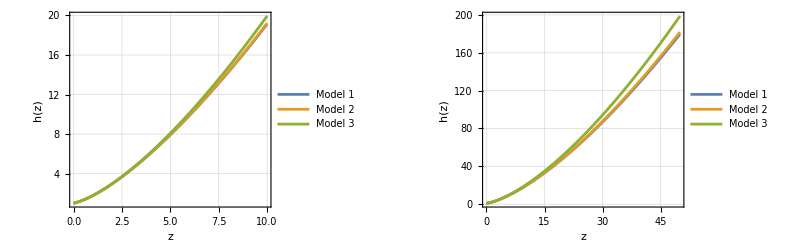

```mathematica
GraphicsRow[{
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zPlot},FrameLabel->{"z","h(z)"},GridLines->Automatic,ImageSize->Full,Frame->True,PlotRange->All,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]],
Plot[{hSolAllSets1[DataSetPlot][z],hSolAllSets2[DataSetPlot][z],hSolAllSets3[DataSetPlot][z]},{z,0,zinitial},FrameLabel->{"z","h(z)"},GridLines->Automatic,Frame->True,PlotRange->All,ImageSize->Full,PlotLegends->Placed[LineLegend[{"Model 1","Model 2","Model 3"},LegendFunction->(Framed[#,FrameStyle->Gray,RoundingRadius->0]&)],{0.8,0.25}]]},ImageSize->Full]
```

## Determining suitable initial conditions for x_in and Ω_in:

#### Classification of eigenvectors:

```mathematica
ClassifyEigenvectors[fp_Association]:=
Module[{eig,vecs,unstableIdx,stableIdx,vq,vxOmega,qComponents},

eig=fp["eigenvalues"];
vecs=fp["eigenvectors"];

unstableIdx=Flatten[Position[eig,_?(Re[#]>0&)]];
stableIdx=Flatten[Position[eig,_?(Re[#]<0&)]];

(*Among the unstable ones,find which has nonzero q-component*)
qComponents=vecs[[unstableIdx,3]];
vq=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]];
vxOmega=vecs[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]];

<|"vq"->vq,"vxOmega"->vxOmega,"vStable"->vecs[[First[stableIdx]]],"lambdaQ"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]>10^-8&)]]]]]]],"lambdaXOmega"->eig[[unstableIdx[[First[Flatten[Position[qComponents,_?(Abs[#]<=10^-8&)]]]]]]]|>];
```

#### Scan of ICs

```mathematica
ScanICs[model_String,dataset_String,c2Range_List]:=
Module[{fp,classified,vq,vxOmega,lambdaQ,qFn,deltaQ,c3,params,results},

fp=matterDominatedFPs[model][dataset];
classified=ClassifyEigenvectors[fp];
vq=classified["vq"];
vxOmega=classified["vxOmega"];
lambdaQ=classified["lambdaQ"];
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
deltaQ=qFn[zinitial]-fp["q"];
c3=deltaQ/vq[[3]];

results=Table[Module[{x0,Ω0,sol,xFn,ΩFn,domainEnd,xFinal,ΩFinal},x0=fp["x"]+c2 vxOmega[[1]]+c3 vq[[1]];
Ω0=fp["Ω"]+c2 vxOmega[[2]]+c3 vq[[2]];
Block[{q,j,s,l,ϵ},
q[zz_]:=qFn[zz];
ϵ=params["eps"];
j[zz_]:=params["j"][zz];
s[zz_]:=Solve[dj,s[zz]][[1,1,2]];
l[zz_]:=Solve[ds,l[zz]][[1,1,2]]//Simplify;
sol=Quiet[Check[NDSolve[{dx,dΩ,x[zinitial]==x0,Ω[zinitial]==Ω0},{x,Ω},{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10],$Failed],NDSolve::ndsz];];
If[sol===$Failed,{c2,x0,Ω0,Indeterminate,Indeterminate,"Failed"},(xFn=x/. sol[[1]];
ΩFn=Ω/. sol[[1]];
domainEnd=xFn["Domain"][[1,1]];
If[domainEnd>0,{c2,x0,Ω0,Indeterminate,Indeterminate,"Diverged at z="<>ToString[domainEnd]},(xFinal=xFn[0];
ΩFinal=ΩFn[0];
{c2,x0,Ω0,xFinal,ΩFinal,If[xFinal<0&&ΩFinal>0,"Physical","Unphysical sign"]})])]],{c2,c2Range}];
results];
```

```mathematica
ScanAllDatasetsPhysical[model_String,c2Range_List]:=Module[{datasets,allResults,physicalRowsByDataset,bounds},datasets=AvailableDatasets[model];
physicalRowsByDataset=Association[Map[Function[dataset,Module[{scanResult,physicalRows},scanResult=ScanICs[model,dataset,c2Range];
physicalRows=Select[scanResult,#[[-1]]==="Physical"&];
dataset->physicalRows]],datasets]];
bounds=Association[Map[Function[dataset,Module[{rows,c2Vals,minRow,maxRow},rows=physicalRowsByDataset[dataset];
If[Length[rows]==0,dataset-><|"c2min"->None,"c2max"->None,"xInAtMin"->None,"OmegaInAtMin"->None,"xInAtMax"->None,"OmegaInAtMax"->None,"count"->0|>,(c2Vals=rows[[All,1]];
minRow=First[Select[rows,#[[1]]==Min[c2Vals]&]];
maxRow=First[Select[rows,#[[1]]==Max[c2Vals]&]];
dataset-><|"c2min"->minRow[[1]],"c2max"->maxRow[[1]],"xInAtMin"->minRow[[2]],"OmegaInAtMin"->minRow[[3]],"xInAtMax"->maxRow[[2]],"OmegaInAtMax"->maxRow[[3]],"count"->Length[rows]|>)]]],datasets]];
allResults=Flatten[Map[Function[dataset,Map[Prepend[#,dataset]&,physicalRowsByDataset[dataset]]],datasets],1];
<|"table"->allResults,"byDataset"->physicalRowsByDataset,"bounds"->bounds|>];
```

### Model 1

#### Initial scan (coarse)

```mathematica
c2TestRange=Join[-Reverse[10^Range[-6,-2,0.2]],10^Range[-6,-2,0.2]];
```

```mathematica
scanResultsModel1=ScanAllDatasetsPhysical["Model 1",c2TestRange];
```

```mathematica
(*Same Grid display as before*)
Grid[Prepend[scanResultsModel1["table"],{"Dataset","c2","x_in","Ω_in","x(0)","Ω(0)","Status"}],Frame->All];
```

```mathematica
Grid[Prepend[Table[{
dataset,
scanResultsModel1["bounds"][dataset]["c2min"],
scanResultsModel1["bounds"][dataset]["c2max"],
scanResultsModel1["bounds"][dataset]["xInAtMin"],
scanResultsModel1["bounds"][dataset]["xInAtMax"],
scanResultsModel1["bounds"][dataset]["OmegaInAtMin"],
scanResultsModel1["bounds"][dataset]["OmegaInAtMax"],
scanResultsModel1["bounds"][dataset]["count"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","c_2(a)","c_2(b)","x_in(a)","x_in(b)","Ω_in(a)","Ω_in(b)","# physical"}],Frame->All]
```

Dataset | c_2(a) | c_2(b) | x_in(a) | x_in(b) | Ω_in(a) | Ω_in(b) | # physical
DESI | -6.30957×10^-6 | 1.58489×10^-6 | -0.0775239 | -0.0775163 | 0.908543 | 0.908541 | 7
Union3 | -2.51189×10^-6 | 3.98107×10^-6 | -0.162502 | -0.162495 | 0.805995 | 0.805994 | 7
Pantheon+ | -2.51189×10^-6 | 3.98107×10^-6 | -0.180313 | -0.180307 | 0.784197 | 0.784196 | 7
DESY5 | -3.98107×10^-6 | 2.51189×10^-6 | -0.128176 | -0.12817 | 0.847708 | 0.847706 | 7
Union3 + Pantheon+ + DESY5 | -2.51189×10^-6 | 3.98107×10^-6 | -0.187076 | -0.18707 | 0.775893 | 0.775891 | 7
Planck | -0.00001 | -1.×10^-6 | 0.0288348 | 0.0288434 | 1.0335 | 1.0335 | 6
Planck + Union3 | -0.00001 | -1.×10^-6 | 0.0196521 | 0.0196607 | 1.02286 | 1.02286 | 6
Planck + Pantheon+ | -0.00001 | -1.×10^-6 | 0.0128567 | 0.0128653 | 1.01497 | 1.01497 | 6
Planck + DESY5 | -0.00001 | -1.×10^-6 | 0.0165296 | 0.0165382 | 1.01924 | 1.01923 | 6
Planck + Union3 + Pantheon+ + DESY5 | -6.30957×10^-6 | -1.×10^-6 | 0.00396443 | 0.00396952 | 1.00462 | 1.00461 | 5

#### Refine Scan:

```mathematica
RefineScan[model_String,dataset_String,scanResults_Association,nPoints_Integer:50]:=Module[{bnds,refinedRange},bnds=scanResults["bounds"][dataset];
If[bnds["min"]===None,Return[$Failed]];
refinedRange=Subdivide[bnds["min"],bnds["max"],nPoints-1];
ScanICs[model,dataset,refinedRange]];
```

## Obtaining Background solutions x(z) and Ω(z)

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

50

```mathematica
(*xin=-10^-14;
Ωin=0.999999997;*)
```

```mathematica
(*Same pertubations away from fixed poitn as 21cm*)
```

```mathematica
δx =10^-14;
δΩ=3*10^-9;
```

```mathematica
Table[qSolAllSets1[dataset][zinitial], {dataset,Keys[qSolAllSets3]}]
```

{0.461211,0.418716,0.40981,0.435881,0.406428,0.514397,0.509806,0.506409,0.508245,0.501962}

```mathematica
Keys[qSolAllSets3]
```

{DESI,Union3,Pantheon+,DESY5,Union3 + Pantheon+ + DESY5,Planck,Planck + Union3,Planck + Pantheon+,Planck + DESY5,Planck + Union3 + Pantheon+ + DESY5}

#### Module

```mathematica
SolveBackground[model_String,dataset_String]:=
Module[{params,qFn,z0,fp,x0,Ω0,q0,sol,xFn,ΩFn,domainEnd},
params=GetParams[model,dataset];
qFn=SolveForq[model,dataset];
z0=zinitial;
fp=matterDominatedFPs[model][dataset];

x0=fp["x"]-δx;
Ω0=fp["Ω"]-δΩ;
q0=qFn[zinitial];

Block[{q,j,s,l,ϵ},
q[z_]=qFn[z];
ϵ=params["eps"];
j[z_]=params["j"][z];
s[z_]=Solve[dj,s[z]][[1,1,2]];
l[z_]=Solve[ds,l[z]][[1,1,2]]//Simplify;
sol=Quiet[NDSolve[{dx,dΩ,x[z0]==x0,Ω[z0]==Ω0},{x,Ω},{z,0,z0},PrecisionGoal->10,AccuracyGoal->10],NDSolve::ndsz][[1]];
xFn=x/. sol;
ΩFn=Ω/. sol;];
domainEnd=xFn["Domain"][[1,1]];

If[domainEnd>0,Print[dataset," is stiff/diverges at z ≃ ",domainEnd]];

<|"x"->xFn,"Ω"->ΩFn,"q"->qFn, "z0"->z0,"zinitial"->zinitial,"failedAtZ"->If[domainEnd>0,domainEnd,None],"x0"->x0,"Ω0"->Ω0, "q0"->q0|>];
```

### Model 1, All datasets

```mathematica
bgResultsModel1=Association[Map[#->SolveBackground["Model 1",#]&,AvailableDatasets["Model 1"]]];
```

DESI is stiff/diverges at z ≃ 0.286452

Union3 is stiff/diverges at z ≃ 0.441852

Pantheon+ is stiff/diverges at z ≃ 0.47417

DESY5 is stiff/diverges at z ≃ 0.381604

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.488118

Planck is stiff/diverges at z ≃ 0.0565262

Planck + Union3 is stiff/diverges at z ≃ 0.0650856

Planck + Pantheon+ is stiff/diverges at z ≃ 0.0706576

Planck + DESY5 is stiff/diverges at z ≃ 0.0678887

Planck + Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.0772577

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel1[dataset]["x0"],
bgResultsModel1[dataset]["Ω0"],
bgResultsModel1[dataset]["q0"],
bgResultsModel1[dataset]["x"][0],
bgResultsModel1[dataset]["Ω"][0],
bgResultsModel1[dataset]["q"][0],
bgResultsModel1[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 1"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -0.0775181 | 0.908561 | 0.461211 | -3.42064×10^48 | 5.63718×10^47 | -0.517033 | 0.286452
Union3 | -0.1625 | 0.806015 | 0.418716 | 1.30235×10^49 | -2.18397×10^48 | -0.46739 | 0.441852
Pantheon+ | -0.180312 | 0.784218 | 0.40981 | 6.35584×10^49 | -1.05944×10^49 | -0.457763 | 0.47417
DESY5 | -0.128173 | 0.847727 | 0.435881 | -1.17581×10^48 | 1.97662×10^47 | -0.488531 | 0.381604
Union3 + Pantheon+ + DESY5 | -0.187075 | 0.775913 | 0.406428 | -1.73663×10^49 | 2.88528×10^48 | -0.455529 | 0.488118
Planck | 0.0288443 | 1.03351 | 0.514397 | 1.55397×10^45 | -2.16431×10^44 | -0.564042 | 0.0565262
Planck + Union3 | 0.0196617 | 1.02287 | 0.509806 | 2.29705×10^45 | -3.28533×10^44 | -0.547098 | 0.0650856
Planck + Pantheon+ | 0.0128663 | 1.01498 | 0.506409 | -1.7523×10^45 | 2.55272×10^44 | -0.533932 | 0.0706576
Planck + DESY5 | 0.0165391 | 1.01925 | 0.508245 | -1.65967×10^45 | 2.39409×10^44 | -0.541286 | 0.0678887
Planck + Union3 + Pantheon+ + DESY5 | 0.00397048 | 1.00463 | 0.501962 | -2.92582×10^46 | 4.35911×10^45 | -0.516172 | 0.0772577

### Model 2, All datasets

```mathematica
bgResultsModel2=Association[Map[#->SolveBackground["Model 2",#]&,AvailableDatasets["Model 2"]]];
```

DESI is stiff/diverges at z ≃ 0.331574

Union3 is stiff/diverges at z ≃ 0.65784

Pantheon+ is stiff/diverges at z ≃ 0.773595

DESY5 is stiff/diverges at z ≃ 0.569033

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.830613

Planck is stiff/diverges at z ≃ 0.0330148

Planck + Union3 is stiff/diverges at z ≃ 0.0474014

Planck + Pantheon+ is stiff/diverges at z ≃ 0.0580478

Planck + DESY5 is stiff/diverges at z ≃ 0.0521417

Planck + Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.0712364

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel2[dataset]["x0"],
bgResultsModel2[dataset]["Ω0"],
bgResultsModel2[dataset]["q0"],
bgResultsModel2[dataset]["x"][0],
bgResultsModel2[dataset]["Ω"][0],
bgResultsModel2[dataset]["q"][0],
bgResultsModel2[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 2"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -0.0683851 | 0.919438 | 0.465769 | -7.76407×10^47 | 1.32811×10^47 | -0.49883 | 0.331574
Union3 | -0.171988 | 0.794417 | 0.413943 | 2.08891×10^50 | -3.73272×10^49 | -0.409006 | 0.65784
Pantheon+ | -0.207 | 0.751359 | 0.396426 | -2.73252×10^49 | 4.80104×10^48 | -0.37856 | 0.773595
DESY5 | -0.144586 | 0.827833 | 0.427652 | 2.22154×10^49 | -3.98352×10^48 | -0.432685 | 0.569033
Union3 + Pantheon+ + DESY5 | -0.223659 | 0.730728 | 0.38809 | -2.3795×10^50 | 4.12872×10^49 | -0.36465 | 0.830613
Planck | 0.0304847 | 1.03541 | 0.51522 | -6.91311×10^44 | 9.3013×10^43 | -0.576389 | 0.0330148
Planck + Union3 | 0.0214876 | 1.02499 | 0.510721 | -2.34344×10^45 | 3.26794×10^44 | -0.556705 | 0.0474014
Planck + Pantheon+ | 0.0146289 | 1.01703 | 0.507292 | -3.86156×10^45 | 5.52476×10^44 | -0.541399 | 0.0580478
Planck + DESY5 | 0.0184722 | 1.02149 | 0.509213 | -2.25381×10^45 | 3.17911×10^44 | -0.550034 | 0.0521417
Planck + Union3 + Pantheon+ + DESY5 | 0.00556607 | 1.00649 | 0.50276 | 1.77375×10^46 | -2.61976×10^45 | -0.520295 | 0.0712364

### Model 3, All datasets

```mathematica
bgResultsModel3=Association[Map[#->SolveBackground["Model 3",#]&,AvailableDatasets["Model 3"]]];
```

DESI is stiff/diverges at z ≃ 0.291899

Union3 is stiff/diverges at z ≃ 0.509532

Pantheon+ is stiff/diverges at z ≃ 0.514173

DESY5 is stiff/diverges at z ≃ 0.39242

Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.522008

Planck + Union3 is stiff/diverges at z ≃ 0.0591791

Planck + Pantheon+ is stiff/diverges at z ≃ 0.117265

Planck + DESY5 is stiff/diverges at z ≃ 0.069151

Planck + Union3 + Pantheon+ + DESY5 is stiff/diverges at z ≃ 0.148878

```mathematica
Grid[Prepend[Table[{
dataset,
bgResultsModel3[dataset]["x0"],
bgResultsModel3[dataset]["Ω0"],
bgResultsModel3[dataset]["q0"],
bgResultsModel3[dataset]["x"][0],
bgResultsModel3[dataset]["Ω"][0],
bgResultsModel3[dataset]["q"][0],
bgResultsModel3[dataset]["failedAtZ"]},{dataset,AvailableDatasets["Model 3"]}],{"Dataset","x(z_i)","Ω(z_i)","q(z_i)","x(0)","Ω(0)","q(0)","Failed at z"}],Frame->All]
```

InterpolatingFunction::dmval: Input value {0} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Dataset | x(z_i) | Ω(z_i) | q(z_i) | x(0) | Ω(0) | q(0) | Failed at z
DESI | -1.×10^-14 | 1. | 0.499945 | 1.89799×10^48 | -3.30723×10^47 | -0.482663 | 0.291899
Union3 | -1.×10^-14 | 1. | 0.499885 | 1.3374×10^49 | -2.64156×10^48 | -0.40775 | 0.509532
Pantheon+ | -1.×10^-14 | 1. | 0.499884 | 5.90285×10^49 | -1.1669×10^49 | -0.408082 | 0.514173
DESY5 | -1.×10^-14 | 1. | 0.499922 | 2.1922×10^48 | -4.07698×10^47 | -0.447329 | 0.39242
Union3 + Pantheon+ + DESY5 | -1.×10^-14 | 1. | 0.499881 | 5.87651×10^49 | -1.16327×10^49 | -0.40875 | 0.522008
Planck | -1.×10^-14 | 1. | 0.49999 | -15.2134 | 2.22807 | -0.638833 | None
Planck + Union3 | -1.×10^-14 | 1. | 0.49998 | -6.86849×10^45 | 9.89759×10^44 | -0.535124 | 0.0591791
Planck + Pantheon+ | -1.×10^-14 | 1. | 0.499972 | -7.72061×10^46 | 1.20838×10^46 | -0.494899 | 0.117265
Planck + DESY5 | -1.×10^-14 | 1. | 0.499978 | -8.81516×10^45 | 1.28958×10^45 | -0.528157 | 0.069151
Planck + Union3 + Pantheon+ + DESY5 | -1.×10^-14 | 1. | 0.499968 | 3.29859×10^47 | -5.36326×10^46 | -0.475607 | 0.148878

## Comparing to 21cm paper

#### Initial conditions

Same initial conditions as the 21cm paper

```mathematica
zinitial
```

50

```mathematica
xin=-10^-14;
Ωin=0.999999997;
```

```mathematica
qin=0.499999996;
Ehin=17346.495;
```

### Model 1

#### Obtaining E(z) and q(z)

```mathematica
params10a["eps"]
```

0.00132349

```mathematica
solq21=NDSolve[{dq/.j->j1/.ϵ->params10a["eps"], q[zinitial]==qin},q,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

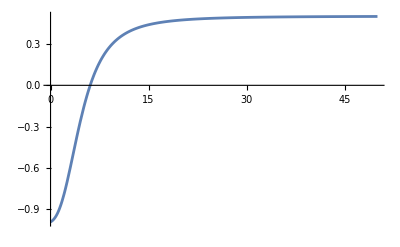

```mathematica
Plot[q[z]/.solq21, {z,0,zinitial}, PlotRange->All]
```

```mathematica
solq21
```

{q→InterpolatingFunction[…]}

```mathematica
dEh/.j->j1/.ϵ->params10a["eps"]/.solq21
```

-Eh[z] (1+InterpolatingFunction[…][z])+(1+z) Eh'[z]==0

```mathematica
solEh21=NDSolve[{dEh/.j->j1/.ϵ->params10a["eps"]/.solq21, Eh[zinitial]==Ehin},Eh,{z,0,zinitial},PrecisionGoal->10,AccuracyGoal->10][[1]];
```

```mathematica
Eh[0]/.solEh21
```

632.412

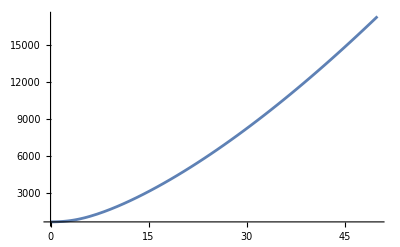

```mathematica
Plot[Eh[z]/.solEh21, {z,0,zinitial}, PlotRange->All]
```